```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

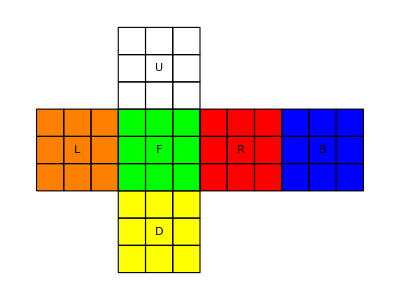

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
```

-Graphics3D-

### Controlli

#### Generale

```mathematica
List[
Button["Load solved",cube3DPieces=GetPieces[sampleStrings["solved"]];],
Button["Load start",cube3DPieces=GetPieces[sampleStrings["start"]];]
]
```

{Load solved,Load start}

#### Mosse standard cubo

```mathematica
List[Button["L",cube3DPieces=RotateL[cube3DPieces];],Button["L'",cube3DPieces=RotateLi[cube3DPieces];],Button["R",cube3DPieces=RotateR[cube3DPieces];],Button["R'",cube3DPieces=RotateRi[cube3DPieces];],Button["U",cube3DPieces=RotateU[cube3DPieces];],Button["U'",cube3DPieces=RotateUi[cube3DPieces];],Button["D",cube3DPieces=RotateD[cube3DPieces];],Button["D'",cube3DPieces=RotateDi[cube3DPieces];],Button["F",cube3DPieces=RotateF[cube3DPieces];],Button["F'",cube3DPieces=RotateFi[cube3DPieces];],Button["B",cube3DPieces=RotateB[cube3DPieces];],Button["B'",cube3DPieces=RotateBi[cube3DPieces];]]
```

{L,L',R,R',U,U',D,D',F,F',B,B'}

#### Rotazione cubo

```mathematica
List[Button["X",cube3DPieces=RotateX[cube3DPieces];],Button["X'",cube3DPieces=RotateXi[cube3DPieces];],Button["Y",cube3DPieces=RotateY[cube3DPieces];],Button["Y'",cube3DPieces=RotateYi[cube3DPieces];],Button["Z",cube3DPieces=RotateZ[cube3DPieces];],Button["Z'",cube3DPieces=RotateZi[cube3DPieces];]]
```

{X,X',Y,Y',Z,Z'}

```mathematica
cube3DPieces = GetPieces[sampleStrings["start"]];

(*Restituisce un cubo nell'insieme totale,a partire dall'elemento*)
getCube[total_,element_]:=(First[Position[total,element]]);

(*Restituisce gli indici dei cubi nell'insieme totale a partire da un pattern in un certo set di elementi riguardante la posizione*)
getPos[total_,elements_,pattern_]:=(idxs=Flatten[Position[Table[Flatten[Cases[{elements[[t]]["pos"]},pattern]],{t,1,Length[elements]}],pattern]];
Return[Flatten[Table[getCube[total,elements[[idxs[[t]]]]],{t,1,Length[idxs]}]]]);

(*Restituisce gli indici dei cubi nell'insieme totale a partire da un pattern in un certo set di elementi riguardante i colori*)
getCol[total_,elements_,pattern_]:=(idxs=Flatten[Position[Table[Flatten[Cases[{elements[[t]]["colors"]},pattern]],{t,1,Length[elements]}],pattern]];
Return[Flatten[Table[getCube[total,elements[[idxs[[t]]]]],{t,1,Length[idxs]}]]]);

(* Restituisce l'indice di un cubo che soddisfa un certo pattern di colori permutati *)
getColSort[total_, elements_,col1_, col2_, col3_] := (Flatten[{
getCol[total,elements,{col1,col2, col3}],getCol[total,elements,{col1,col3, col2}],getCol[total,elements,{col2,col1, col3}],
getCol[total,elements,{col3,col1, col2}],getCol[total,elements,{col3,col2, col1}],getCol[total,elements,{col2,col3, col1}]}])

(*Inserisce un white edge al second floor nella faccia superiore*)
setSFDaisy[SFWhiteEdge_]:=(checkW=SFWhiteEdge["colors"][[1]]=="W"; Switch[SFWhiteEdge["pos"],
{1,0,1},(If[checkW,cube3DPieces=RotateFi[cube3DPieces],cube3DPieces=RotateR[cube3DPieces]]),
{1,0,-1},(If[checkW,cube3DPieces=RotateB[cube3DPieces],cube3DPieces=RotateRi[cube3DPieces]]),
{-1,0,1},(If[checkW,cube3DPieces=RotateF[cube3DPieces],cube3DPieces=RotateLi[cube3DPieces]]),
{-1,0,-1},(If[checkW,cube3DPieces=RotateBi[cube3DPieces],cube3DPieces=RotateL[cube3DPieces]])])

getSingleColor[element_, color1_, color2_]:=Intersection[Cases[element["colors"],Except[color1]], Cases[element["colors"], Except[color2]]]
```

```mathematica
(*Specifica dei numeri di facce none per ogni cubo nell'insieme cube3DPieces,per riconoscere corner,edges e centers*)numberOfNone:=Table[Count[cube3DPieces[[t]]["colors"],None],{t,1,Length[cube3DPieces]}];

(*Ricerca degli edges bianchi*)
idxOfEdges:=Flatten[Position[numberOfNone,1]];
idxWhiteEdges:=getCol[cube3DPieces,cube3DPieces[[idxOfEdges]],{___,"W",___}];
whiteEdges:=cube3DPieces[[idxWhiteEdges]]

(*Ricerca dei petali che devono diventare bianchi*)
idxPetali:=Flatten[{Flatten[getPos[cube3DPieces,cube3DPieces,{1|-1,1,0}]],Flatten[getPos[cube3DPieces,cube3DPieces,{0,1,1|-1}]]}];
petali := cube3DPieces[[idxPetali]]
(* Specifica dei petali che hanno già una faccia superiore bianca *)
rightPetali := cube3DPieces[[getCol[cube3DPieces,petali,{_,"W",_}]]]
```

```mathematica
(* Controlla il cubo nella faccia superiore rispetto ad una faccia bianca *)
getWTop[element_] := Switch[element["pos"][[2]],
1,  element, (*devo trasformarlo in un 2F ma il top è lui *)
0, If[ MatchQ[element["colors"],{_,_,"W"}], (* Faccia bianca o su Front-Back o su Left-Right *)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{element["pos"][[1]],1,0}]]]] ,(*FB mantengo X*)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{0,1,element["pos"][[3]]}]]] ](*LR mantengo Z*)
],
-1, If[MatchQ[element["colors"],{_,"W",_}], (* Faccia bianca o su Up-Down o su Front-Back *)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{element["pos"][[1]],1,element["pos"][[3]]}]]] ], (*UD mantengo Z e X*)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{element["pos"][[1]],1,element["pos"][[3]]}]]]]  (*FB devo trasformarlo in un 2F prima, quindi controllo solo quella sopra, ma andrà fatto un doppio controllo*)
]
]

(* Da chiamare dopo aver fatto i giusti check con getWTop, rende un edge con una faccia bianca un edge da 2o piano *)
makeSF[element_] := 
(While[getWTop[element]["colors"][[2]] == "W", cube3DPieces = RotateU[cube3DPieces]];
Switch[element["pos"][[1]],
   0, If[element["pos"][[3]] == -1, cube3DPieces = RotateB[cube3DPieces], cube3DPieces = RotateF[cube3DPieces]], (* Se dietro, B, se davanti, F*)
   1, cube3DPieces = RotateR[cube3DPieces], (* se a dx, R *)
-1, cube3DPieces = RotateL[cube3DPieces] (* se a sx, L *)
];
)

(* Gli edges da inserire sono quelli che non fanno ancora parte dei petali al posto giusto *)
leftEdges := Complement[whiteEdges, rightPetali]
```

```mathematica
(* 
	 Finché ci sono dei leftEdges, mi salvo i colori del cubetto che sto considerando così gli assegno un cubetto senza che cambi in continuazione. Poi, finché questo cubetto
	non fa parte dei rightPetali, lo rendo un second floor, libero il cubo in alto da una faccia bianca facendo quante UP servono e faccio la mossa giusta per portarlo in alto
	con setSFDaisy
*)

While[Length[leftEdges] != 0,
 {col1,col2,col3}= First[cube3DPieces[[getCube[cube3DPieces,First[leftEdges]]]]]["colors"];
 edge:= First[cube3DPieces[[getColSort[cube3DPieces,cube3DPieces,col1,col2,col3]]]];
While[Intersection[List[edge],rightPetali] == {},
If[edge["pos"][[2]] != 0,makeSF[edge]];
While[getWTop[edge]["colors"][[2]] == "W", cube3DPieces = RotateU[cube3DPieces]];
setSFDaisy[edge];
];
]
(* Ottengo gli id dei centri su tutte le facce che non sono sopra e sotto *)
idxCenters = Flatten[Position[numberOfNone,2]];
centers = cube3DPieces[[idxCenters]];
lateralCenters = Complement[centers ,cube3DPieces[[getColSort[cube3DPieces,centers,None,None,"W"|"Y"]]]];
(* Per ogni elemento del petalo... *)
For[i=1, i<5, i++, (
(* Trova il centro di riferimento *)
currentCenter := lateralCenters[[i]];
(* Trova il cubo da operare *)
cubeAboveId := First[getPos[cube3DPieces, cube3DPieces, {currentCenter["pos"][[1]],currentCenter["pos"][[2]]+1,currentCenter["pos"][[3]]}]];
(* Finchè il colore del cubo non combacia con quello di centro faccia ruota in senso orario il top layer *)
While[getSingleColor[cube3DPieces[[cubeAboveId]],"W",None]!=getSingleColor[currentCenter, None, None],(cube3DPieces = RotateU[cube3DPieces];)];
(* Scaravolta la croce *)
Switch[First[getSingleColor[cube3DPieces[[cubeAboveId]],"W",None]], 
"O",(cube3DPieces=RotateL[RotateL[cube3DPieces]]),
"B",(cube3DPieces=RotateF[RotateF[cube3DPieces]]),
"G",(cube3DPieces=RotateB[RotateB[cube3DPieces]]),
"R",(cube3DPieces=RotateR[RotateR[cube3DPieces]])]
)]
cube3DPieces=RotateZ[RotateZ[cube3DPieces]];
(* Se tutto è andato come doveva ora la croce è comparsa sulla faccia bianca.  *)
```

```mathematica
idxCorners := Flatten[Position[numberOfNone,0]];
corners := cube3DPieces[[idxCorners]]
whiteCorners := cube3DPieces[[getCol[cube3DPieces, cube3DPieces[[idxCorners]],{___,"W",___}]]]

frontFaceColor := First[cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{0,0,1}]]]]["colors"][[3]]
rightFaceColor:= First[cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{1,0,0}]]]]["colors"][[1]]
leftFaceColor:= First[cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{-1,0,0}]]]]["colors"][[1]]
topFaceColor := First[cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{0,1,0}]]]]["colors"][[2]]

rightTopCorner := cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,1}]]]]
rightBottomCorner := cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,-1,1}]]]]
topCorners := cube3DPieces[[getPos[cube3DPieces,corners,{_,1,_}]]]

cornerToPlace := cube3DPieces[[First[getColSort[cube3DPieces,corners,frontFaceColor,rightFaceColor,topFaceColor]]]]
```

```mathematica
(*R'D'RD*)
For[i=1, i<5, i++, (
If[cornerToPlace["pos"][[2]]==1,
Switch[cornerToPlace["pos"],
{1,1,-1},cube3DPieces = RotateB[RotateDi[RotateBi[cube3DPieces]]],
{1,1,1},cube3DPieces = RotateFi[RotateDi[RotateF[cube3DPieces]]],
{-1,1,1},cube3DPieces = RotateF[RotateDi[RotateFi[cube3DPieces]]],
{-1,1,-1}, cube3DPieces = RotateBi[RotateDi[RotateB[cube3DPieces]]]
]];
While[cornerToPlace != rightBottomCorner, cube3DPieces = RotateD[cube3DPieces]];
While[cornerToPlace != rightTopCorner || rightTopCorner["colors"][[2]]!="W", cube3DPieces = RotateD[RotateR[RotateDi[RotateRi[cube3DPieces]]]]];
cube3DPieces=RotateY[cube3DPieces] 
)
]
```

```mathematica
cube3DPieces=RotateZ[RotateZ[cube3DPieces]];
```

```mathematica
edges := cube3DPieces[[idxOfEdges]]

prova[colors_] := If[colors[[1]] == None, colors[[3]],colors[[1]]]

leftEdge := cube3DPieces[[First[getColSort[cube3DPieces,edges,frontFaceColor,leftFaceColor,None]]]];
rightEdge := cube3DPieces[[First[getColSort[cube3DPieces,edges,frontFaceColor,rightFaceColor,None]]]];

(* Deve andare a destra   ->  U R U' R' U' F' U F 
Deve andare a sinistra ->  U' L' U L U F U' F'*)

checkSF := {
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,0,1}]]]]["colors"][[3]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,0,1}]]]]["colors"][[3]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,0,1}]]]]["colors"][[3]],

cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,0,-1}]]]]["colors"][[3]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,0,-1}]]]]["colors"][[3]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,0,-1}]]]]["colors"][[3]],

cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,0,-1}]]]]["colors"][[1]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,0,0}]]]]["colors"][[1]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,0,1}]]]]["colors"][[1]],

cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,0,-1}]]]]["colors"][[1]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,0,0}]]]]["colors"][[1]] == 
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,0,1}]]]]["colors"][[1]]
}

While[
Total[Boole[checkSF]] != 4,
(
(* Proviamo a controllare se per ogni lato abbiamo nel layer più in alto un edge da inserire*)
For[i=1, i<5, i++, (
If[leftEdge["pos"][[2]]!=1 && rightEdge["pos"][[2]]!=1 ,cube3DPieces=RotateY[cube3DPieces]];
)];

topCube := cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,1,1}]]]];

(* Se non ci sono edge da inserire, facciamo una mossa a vuoto per liberarne uno *)
If[leftEdge["pos"][[2]]!=1 && rightEdge["pos"][[2]]!=1,
cube3DPieces = RotateFi[RotateUi[RotateF[RotateU[RotateL[RotateU[RotateLi[RotateUi[cube3DPieces]]]]]]]],

(* altrimenti o c'è un leftEdge, e salviamo i suoi colori *)
If[leftEdge["pos"][[2]]==1 , 
prova2 = prova[leftEdge["colors"]]; (* colore della faccia che gestirà l'edge sinistro da inserire... *)
altroColore = leftEdge["colors"][[2]], (* ...e quello che sta invece sopra*)
(* o un rightEdge e salviamo i suoi *)
prova2 = prova[rightEdge["colors"]]; (* colore della faccia che gestirà l'edge destro da inserire... *)
altroColore = rightEdge["colors"][[2]] (* ...e quello che sta invece sopra*)
];

While [frontFaceColor != prova2, cube3DPieces = RotateY[cube3DPieces]]; (* Mettiamo di fronta la faccia su cui lavorare *)

(* Ruotiamo il layer superiore finché l'edge da inserire non è sopra il centro considerato *)
While[ topCube["colors"][[3]]!=frontFaceColor||topCube["colors"][[2]]!=altroColore,cube3DPieces = RotateU[cube3DPieces]];

(* Ora se l'edge considerato è un left, facciamo le relative mosse, altrimenti quelle dei right*)
If[altroColore == leftFaceColor,
cube3DPieces = RotateFi[RotateUi[RotateF[RotateU[RotateL[RotateU[RotateLi[RotateUi[cube3DPieces]]]]]]]],
cube3DPieces = RotateF[RotateU[RotateFi[RotateUi[RotateRi[RotateUi[RotateR[RotateU[cube3DPieces]]]]]]]]]
]
)
]
```

```mathematica
While[frontFaceColor != "B", cube3DPieces=RotateY[cube3DPieces]]
topFace := Union[cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{0,1,_}]]], cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{_,1,0}]]]]
nYellow := Length[cube3DPieces[[getCol[cube3DPieces,topFace,{_,"Y",_}]]]]
```

```mathematica
(* F R U R' U' F' *)

(* Cubi da sopra in senso orario:
   0, 1,-1
    1, 1, 0	<3
   0, 1, 1
   -1, 1, 0    <3
*)

If[nYellow<3, cube3DPieces = RotateFi[RotateUi[RotateRi[RotateU[RotateR[RotateF[cube3DPieces]]]]]]]
If[nYellow == 3,
While[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,0}]]]]["colors"][[2]] != "Y" || cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,0}]]]]["colors"][[2]] != "Y" ,
If[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,1,-1}]]]]["colors"][[2]] == "Y" && cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,1,1}]]]]["colors"][[2]] == "Y", cube3DPieces = RotateF[cube3DPieces],
While[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,1,-1}]]]]["colors"][[2]] != "Y" || cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,0}]]]]["colors"][[2]] != "Y" ,cube3DPieces = RotateF[cube3DPieces] ];
cube3DPieces = RotateFi[RotateUi[RotateRi[RotateU[RotateR[RotateF[cube3DPieces]]]]]]
]
];
cube3DPieces = RotateFi[RotateUi[RotateRi[RotateU[RotateR[RotateF[cube3DPieces]]]]]];
]
```

```mathematica
backFaceColor := First[cube3DPieces[[getPos[cube3DPieces,cube3DPieces,{0,0,-1}]]]]["colors"][[3]]
checkY := {
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,1,1}]]]]["colors"][[3]] == frontFaceColor,
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,0}]]]]["colors"][[1]] == rightFaceColor,
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{0,1,-1}]]]]["colors"][[3]] == backFaceColor,
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,0}]]]]["colors"][[1]] ==leftFaceColor
}

While[Total[Boole[checkY]] != 4,
While[
Total[Boole[checkY]] != 2,
cube3DPieces = RotateU[cube3DPieces]
];

While[
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,0}]]]]["colors"][[1]] == leftFaceColor,
cube3DPieces = RotateY[cube3DPieces]
];

(* R U R' U R U U R' U *)
cube3DPieces = RotateU[RotateRi[RotateU[RotateU[RotateR[RotateU[RotateRi[RotateU[RotateR[cube3DPieces]]]]]]]]];
]
```

```mathematica
(*
	 1,1,1 <3 davanti a destra
  -1,1,1 davanti a sinistra
	1,1,-1 dietro a destra
   -1,1,-1 dietro a sinistra
*)

checkCorners := {
Sort[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,1}]]]]["colors"]] == Sort[{frontFaceColor, rightFaceColor,"Y"}],
Sort[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,1}]]]]["colors"]] == Sort[{frontFaceColor, leftFaceColor,"Y"}],
Sort[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,-1}]]]]["colors"]] == Sort[{backFaceColor, rightFaceColor,"Y"}],
Sort[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,-1}]]]]["colors"]] == Sort[{backFaceColor, leftFaceColor,"Y"}]
}

(* U R U' L' U R' U' L *)
While[Total[Boole[checkCorners]] == 0,
cube3DPieces = RotateL[RotateUi[RotateRi[RotateU[RotateLi[RotateUi[RotateR[RotateU[cube3DPieces]]]]]]]]
]

While[
Sort[cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,1}]]]]["colors"]] != Sort[{frontFaceColor, rightFaceColor,"Y"}],
cube3DPieces = RotateY[cube3DPieces]
]

While[Total[Boole[checkCorners]] == 1,
cube3DPieces = RotateL[RotateUi[RotateRi[RotateU[RotateLi[RotateUi[RotateR[RotateU[cube3DPieces]]]]]]]]
]
```

```mathematica
checkOrientation := {
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,1}]]]]["colors"] == {rightFaceColor, "Y", frontFaceColor},
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,1}]]]]["colors"] == {leftFaceColor, "Y", frontFaceColor},
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,-1}]]]]["colors"] == {rightFaceColor, "Y", backFaceColor},
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{-1,1,-1}]]]]["colors"] == {leftFaceColor, "Y", backFaceColor}
}

(* R' D' R D *)

While[Total[Boole[checkOrientation]] != 4,
While[
cube3DPieces[[First[getPos[cube3DPieces,cube3DPieces,{1,1,1}]]]]["colors"] != {_, "Y", _},
cube3DPieces = RotateD[RotateR[RotateDi[RotateRi[cube3DPieces]]]]
];
cube3DPieces = RotateU[cube3DPieces]
]
```